```mathematica
compOnlyEdges = Flatten@Map[Thread,Table[Map[Thread,articles[[i]]-> Intersection[Keys[compData],compData[[i]][["LinksList"]]]],{i,1,100}]];
```

```mathematica
CommunityGraphPlot[compOnlyEdges,VertexLabels->Placed[Automatic,Tooltip],Method->"Hierarchical"]
```

-Graphics-

```mathematica
compOnlySingle =Union@Flatten@Append[compOnlyEdges,Table[Keys[compData][[i]]->Keys[compData][[i]],{i,Length[Keys[compData]]}]];
```

```mathematica
CommunityGraphPlot[compOnlySingle,VertexLabels->Placed[Automatic,Tooltip],Method->"Hierarchical"]
```

-Graphics-

```mathematica
noLinks = Complement[Keys[compData],Flatten@FindGraphCommunities[compOnlyEdges]];
```

```mathematica
CommunityGraphPlot[compOnlyEdges,FindGraphCommunities[compOnlyEdges,Method->#],VertexLabels->Placed[Automatic,Tooltip],ImageSize->Medium]&/@{"Modularity","Centrality","CliquePercolation","Hierarchical","Spectral","VertexMoving"}//Row
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
CommunityGraphPlot[compOnlyEdges,FindGraphCommunities[compOnlyEdges,Method->#],VertexLabels->Placed[Automatic,Tooltip],ImageSize->Medium]&/@{"Modularity","VertexMoving"}//Row
```

-Graphics--Graphics-

```mathematica
FindGraphCommunities[compOnlyEdges]===FindGraphCommunities[compOnlyEdges,Method->"Modularity"]
```

True

```mathematica
FindGraphCommunities[compOnlyEdges]
```

{{Computational chemistry,Computational and Theoretical Chemistry,Computational Chemistry List,Computational complexity theory,Computational engineering,Computational geometry,Computational mathematics,Computational social science,Computational Chemistry Grid,Computational problem,Computational Diffie–Hellman assumption,Computational topology,Computational hardness assumption,Computational group theory,Computational social choice},{Computational anatomy,Computational mechanics,Computational science,Computational history,Computational criminology,Computational geophysics,Computational Infrastructure for Geodynamics,Computational statistics,Computational electromagnetics,Computational informatics,Computational law,Computational scientist,Computational Science & Discovery,Computational Statistics & Data Analysis},{Computational and Statistical Genetics,Computational biology,Computational genomics,Computational and Systems Neuroscience,Computational neuroscience,Computational phylogenetics,Computational Biology and Chemistry,Computational epistemology,Computational learning theory,Computational epigenetics,Computational immunology,Computational-representational understanding of mind,Computational X,Computational thinking},{Computational linguistics,Computational cognition,Computational model,Computational resource,Computational creativity,Computational humor,Computational lexicology,Computational semantics,Computational semiotics,Computational visualistics},{Computational archaeology,Computational sociology,Computational intelligence,Computational cybernetics,Computational Heuristic Intelligence,Computational economics,Computational finance,Computational knowledge economy,Computational epidemiology},{Computational aeroacoustics,Computational fluid dynamics,Computational physics,Computational astrophysics,Computational thermodynamics,Computational magnetohydrodynamics,Computational particle physics},{Computational complexity,Computational complexity of mathematical operations,Computational number theory},{Computational photography,Computational photography (artistic)}}

```mathematica
groups=Association[
	Flatten[
		Map[
			Thread,
			Thread[
				FindGraphCommunities[compOnlyEdges]->
				{
					"Computational Chemistry Group",
					"Computational Science and Data Group",
					"Computational Biology Group",
					"Computational Thinking/Sentience Group",
					"Computational Intelligence and Economics Group",
					"Computational Physics Group",
					"Computational Complexity Group",
					"Computational Photography Group"
				}
			]
		]
	]
];
```

```mathematica
groupsEdges=Table[Replace[compOnlyEdges[[i]],compOnlyEdges[[i]]-> (groups[compOnlyEdges[[i]][[1]]]-> groups[compOnlyEdges[[i]][[2]]])],{i,Length[compOnlyEdges]}];
```

```mathematica
GraphPlot[groupsEdges,SelfLoopStyle->None,VertexLabeling->Tooltip,ImageSize->Large]
```

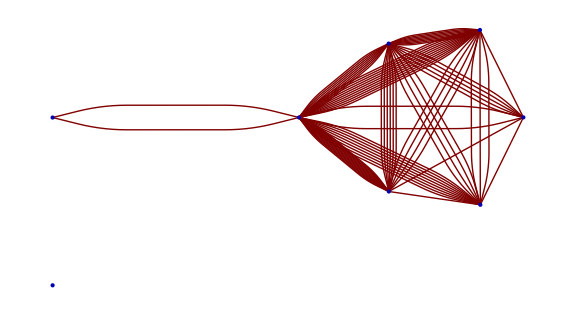

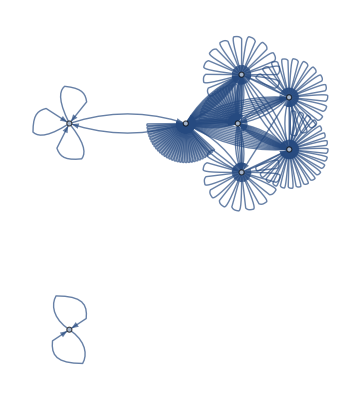

```mathematica
Graph[groupsEdges,VertexLabels->Placed[Automatic,Tooltip]]
```

```mathematica
CommunityGraphPlot[groupsEdges]
```

-Graphics-

```mathematica
CommunityGraphPlot[groupsEdges,FindGraphCommunities[groupsEdges,Method->#],VertexLabels->Placed[Automatic,Tooltip],ImageSize->Small]&/@{"Modularity","Centrality","CliquePercolation","Hierarchical","Spectral"}//Row
```

-Graphics--Graphics--Graphics--Graphics--Graphics-